## Magnetic Field Calculator for Stern-Gerlach

```mathematica
Button["Open Field Calculator",MagnetDialog]
```

Open Field Calculator

```mathematica
?B
```

B[I] calculates the magnetic field (in Tesla) for magnet current I (amps).

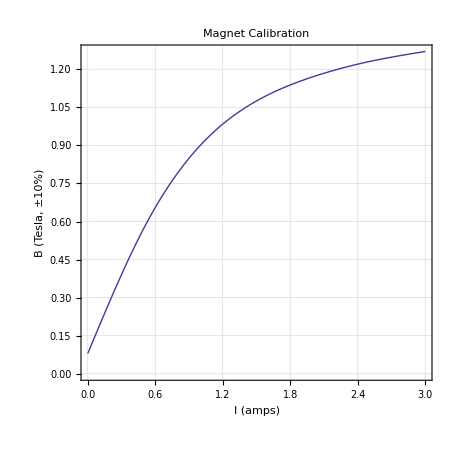

```mathematica
Bplot
```

## Initialization Code

### This data comes from the original chart

```mathematica
data={{0,0.08},{0.5,0.575},{1.,0.9},{1.5,1.075},{2.,1.17},{2.5,1.23},{3.,1.27}};
```

### Fit a cubic spline to the data

```mathematica
Needs["Splines`"]
```

```mathematica
spline=SplineFit[data,Cubic];
```

### Define a function which, given I, calculates B

```mathematica
B[x_?NumberQ]:=spline[2 x][[2]]/;0≤x&&x≤3
B::usage="B[I] calculates the magnetic field (in Tesla) for magnet current I (amps)."
```

B[I] calculates the magnetic field (in Tesla) for magnet current I (amps).

```mathematica
Bplot=Plot[{B[x]},{x,0,3},AspectRatio->1,Frame->True,PlotLabel->Style["Magnet Calibration",Larger],GridLines->Automatic,GridLinesStyle->GrayLevel[.85],PlotStyle->Thick,FrameLabel->{Style["I (amps)",Larger,Italic],Style["B (Tesla, ±10%)",Larger,Italic]},ImageSize->450];
```

### Here is a dynamic calculator of B vs. I in a dialog window

```mathematica
MagnetFieldNotebook=Notebook[{}];
```

```mathematica
MagnetDialog :=If[MagnetFieldNotebook===Notebook[{}],
MagnetFieldNotebook=CreateDialog[
{Manipulate[
Block[{b},
b=B[x];
Grid[{
{Tooltip[Style["Magnet Field (Tesla): ",FontFamily->"Helvetica"],"The magnetic field estimate from the calibration data"],Tooltip[Style[ToString[ Round[b,.001]],FontFamily->"Helvetica"],"The magnetic field estimate from the calibration data"]},{},{Style["Calibration has a ±10% systematic scale uncertainty",FontFamily->"Helvetica"],SpanFromLeft}
},Alignment->{Left,Baseline}](* Grid *)
](* Block *),
Style["Enter Magnet Current (Amps):",Larger],"",
{{x,1.0,
"Magnet Current (Amps)"}
,ControlType->InputField},
AppearanceElements->None](* Manipulate *)
},
Magnification->1.5,
Deployed->True,ShowCellBracket->False,Saveable->False,
WindowSize->All (*,WindowFrame->"Normal",WindowElements->"MagnificationPopUp" *),WindowFloating->False,
WindowTitle->"Magnet Calculator - Physics 7 Stern-Gerlach",
NotebookEventActions->{"WindowClose":>(MagnetFieldNotebook=Notebook[{}];)}
];,SetSelectedNotebook[MagnetFieldNotebook]];
```

```mathematica
data=Import["/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/corrected_Zmax.dat"]
```

{{S,Detector_current(10^-13A),Corrected_Zmax(mm)},{0.459,0.356},{0.459,0.352},{0.459,0.344},{1.203,0.261},{1.203,0.261},{1.203,0.256},{0.341,0.286},{0.341,0.277},{0.341,0.291},{0.851,0.563},{0.851,0.542},{0.851,0.573},{2.183,0.867},{2.183,0.788},{2.183,0.871}}

```mathematica
modData=Join[{data[[1]]},Table[{B[data[[i]][[1]]],data[[i]][[2]]},{i,2,Length[data]}]]
```

{{S,Detector_current(10^-13A),Corrected_Zmax(mm)},{0.539632,0.356},{0.539632,0.352},{0.539632,0.344},{0.985027,0.261},{0.985027,0.261},{0.985027,0.256},{0.430783,0.286},{0.430783,0.277},{0.430783,0.291},{0.821991,0.563},{0.821991,0.542},{0.821991,0.573},{1.19494,0.867},{1.19494,0.788},{1.19494,0.871}}

```mathematica
Export["/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/finalZmax.dat",modData]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/finalZmax.dat